```mathematica
Fx[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Piecewise[{{sy Sin[Abs[(x-x0)/sx]]/((x-x0)/sx)^2+y0,x≠x0}},sy];
Gx[x_?NumberQ,e_?NumberQ/;e>1,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Piecewise[{{sy*ⅇ^(-e((x-x0)/sx)^2)+y0,x≠x0}},sy];
Ix[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Piecewise[{{sy(2 BesselJ[1,(x-x0)/sx]/((x-x0)/sx))^2+y0,x≠x0}},sy];
Lx[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=sy 1/(1+((x-x0)/sx)^2)+y0;
Fmx[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Min[Piecewise[{{sy Sin[Abs[(x-x0)/sx]]/((x-x0)/sx)^2+y0,x≠x0}},sy],255];
Gmx[x_?NumberQ,e_?NumberQ/;e>1,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Min[Piecewise[{{sy*ⅇ^(-e((x-x0)/sx)^2)+y0,x≠x0}},sy],255];
Imx[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Min[Piecewise[{{sy(2 BesselJ[1,(x-x0)/sx]/((x-x0)/sx))^2+y0,x≠x0}},sy],255];
Lmx[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ]=Min[sy 1/(1+((x-x0)/sx)^2)+y0,255];
Ix3D[x_?NumberQ,y_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ]=Piecewise[{{sz(2 BesselJ[1,√(((x-x0)/sx)^2+((y-y0)/sy)^2)]/(√(((x-x0)/sx)^2+((y-y0)/sy)^2)))^2+z0,x≠x0||y≠y0}},sz];
Imx3D[x_?NumberQ,y_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ]=Min[Piecewise[{{sz(2 BesselJ[1,√(((x-x0)/sx)^2+((y-y0)/sy)^2)]/(√(((x-x0)/sx)^2+((y-y0)/sy)^2)))^2+z0,x≠x0||y≠y0}},sz],255];Gx3D[x_?NumberQ,y_?NumberQ,e_?NumberQ/;e>1,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ]=Piecewise[{{sz*ⅇ^(-e(((x-x0)/sx)^2+((y-y0)/sy)^2))+z0,x≠x0||y≠y0}},sz];
Gmx3D[x_?NumberQ,y_?NumberQ,e_?NumberQ/;e>1,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ]=Min[Piecewise[{{sz*ⅇ^(-e(((x-x0)/sx)^2+((y-y0)/sy)^2))+z0,x≠x0||y≠y0}},sz],255];
Fx3D[x_?NumberQ,y_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ]=Piecewise[{{sz Sin[√(((x-x0)/sx)^2+((y-y0)/sy)^2)]/(((x-x0)/sx)^2+((y-y0)/sy)^2)+z0,x≠x0||y≠y0}},sz];
Fmx3D[x_?NumberQ,y_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ]=Min[Piecewise[{{sz Sin[√(((x-x0)/sx)^2+((y-y0)/sy)^2)]/(((x-x0)/sx)^2+((y-y0)/sy)^2)+z0,x≠x0||y≠y0}},sz],255];
```

```mathematica
Manipulate[Plot[Bx[x,sx,sy,x0,y0],{x,-10,10},PlotRange->{0,255}],{{sx,1},0,10},{{sy,255},0,1024},{{x0,0},-10,10},{{y0,0},-64,64}]
```

```mathematica
Manipulate[DensityPlot[Ix3D[x,y,sx,sy,sz,x0,y0,z0],{x,-32,32},{y,-32,32},PlotRange->{0,255},PlotPoints->50],{sx,1,20},{e,1.1,10},{sy,1,20},{{sz,6000},0,100000},{{x0,0},-10,10},{{y0,0},-10,10},{{z0,0},-255,255}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of System`SampledPlotsDump`dataextremes$20971.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of System`SampledPlotsDump`dataextremes$21550.

```mathematica
observation = Import["C:\\Users\\Benjamin\\OneDrive\\Documents\\UQAR\\2017 Été\\Stage I\\mathematica-test\\points.data", "Table"];
X=observationᵀ⟦1⟧;
Y=observationᵀ⟦2⟧;
N[m=(X.(Y-0))/Total[Y-0]]
fittedFx=NonlinearModelFit[Y,Fx[x,sx,sy,x0,y0],{{sx,24},{sy,32},{x0,m}, {y0,20}},x]
fittedGx=NonlinearModelFit[Y,Gx[x,e,sx,sy,x0,y0],{{e,2},{sx,7},{sy,255},{x0,m}, {y0,0}},x]
fittedIx=NonlinearModelFit[Y,Ix[x,sx,sy,x0,y0],{{sx,7},{sy,255},{x0,m}, {y0,0}},x]
fittedLx=NonlinearModelFit[Y,Lx[x,sx,sy,x0,y0],{{sx,7},{sy,255},{x0,m}, {y0,0}},x]
fittedFmx=NonlinearModelFit[Y,Fmx[x,sx,sy,x0,y0],{{sx,7},{sy,255},{x0,m}, {y0,0}},x]
fittedGmx=NonlinearModelFit[Y,Gmx[x,e,sx,sy,x0,y0],{{e,1.01},{sx,7},{sy,255},{x0,m}, {y0,0}},x]
fittedImx=NonlinearModelFit[Y,{Imx[x,sx,sy,x0,y0],{sx>0,sy>0}},{{sx,7},{sy,1024},{x0,m}, {y0,0}},x]
fittedLmx=NonlinearModelFit[Y,{Lmx[x,sx,sy,x0,y0],{sy>0,y0>0}},{{sx,0.1},{sy,1024},{x0,m}, {y0,0}},x]
```

130.123

NonlinearModelFit::nrlnum: The function value {-2.+Fx[1.,-6.31259,58.4695,130.188,34.4562],-3.+Fx[2.,-6.31259,58.4695,130.188,34.4562],-2.+Fx[3.,-6.31259,58.4695,130.188,34.4562],-5.+Fx[4.,-6.31259,58.4695,130.188,34.4562],«43»,-5.+Fx[48.,-6.31259,58.4695,130.188,34.4562],-3.+Fx[49.,-6.31259,58.4695,130.188,34.4562],-3.+Fx[50.,-6.31259,58.4695,130.188,34.4562],«206»} is not a list of real numbers with dimensions {256} at {sx,sy,x0,y0} = {-6.31259,58.4695,130.188,34.4562}.

FittedModel[Fx[x,-6.31259,58.4695,130.188,34.4562]]

NonlinearModelFit::ivar: … is not a valid variable.

NonlinearModelFit[{2,3,2,5,3,3,3,3,3,3,2,5,2,2,3,3,3,1,3,2,3,3,3,5,5,5,3,3,2,3,2,2,3,3,2,3,5,3,3,3,3,5,3,5,3,3,3,5,3,3,3,3,3,2,3,3,5,3,7,5,3,5,3,5,5,7,5,5,3,6,5,6,6,5,5,6,5,6,7,3,3,6,7,9,8,3,5,6,8,8,7,6,8,14,13,15,10,13,16,24,24,16,16,17,27,29,27,21,21,40,73,84,112,85,105,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,248,143,64,37,41,50,51,34,30,30,49,49,49,35,16,12,17,20,19,13,9,10,10,12,12,8,7,9,9,7,6,5,6,6,7,6,6,6,5,5,5,6,5,5,6,3,3,6,3,5,5,3,3,3,3,5,7,5,2,3,3,6,3,2,3,3,5,2,3,3,3,3,3,3,3,2,2,3,3,5,3,2,5,2,2,5,3,3,3,3,3,3,2,2,1,3,3,2,2,3,5,2,2,2,2,1,2,2,2,3},1,1,x]
 |  |  |  |

FittedModel[Ix[x,9.97282,288.753,131.385,2.78753]]

FittedModel[Lx[x,15.005,311.542,131.399,-12.2048]]

FittedModel[Fmx[x,9.44171,440.077,131.398,7.69605]]

NonlinearModelFit::ivar: … is not a valid variable.

NonlinearModelFit[{2,3,2,5,3,3,3,3,3,3,2,5,2,2,3,3,3,1,3,2,3,3,3,5,5,5,3,3,2,3,2,2,3,3,2,3,5,3,3,3,3,5,3,5,3,3,3,5,3,3,3,3,3,2,3,3,5,3,7,5,3,5,3,5,5,7,5,5,3,6,5,6,6,5,5,6,5,6,7,3,3,6,7,9,8,3,5,6,8,8,7,6,8,14,13,15,10,13,16,24,24,16,16,17,27,29,27,21,21,40,73,84,112,85,105,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,248,143,64,37,41,50,51,34,30,30,49,49,49,35,16,12,17,20,19,13,9,10,10,12,12,8,7,9,9,7,6,5,6,6,7,6,6,6,5,5,5,6,5,5,6,3,3,6,3,5,5,3,3,3,3,5,7,5,2,3,3,6,3,2,3,3,5,2,3,3,3,3,3,3,3,2,2,3,3,5,3,2,5,2,2,5,3,3,3,3,3,3,2,2,1,3,3,2,2,3,5,2,2,2,2,1,2,2,2,3},1,1,x]
 |  |  |  |

FittedModel[Imx[x,6.10525,1429.67,131.333,4.15606]]

FittedModel[Lmx[x,0.139718,1.91357×10^6,131.398,0.]]

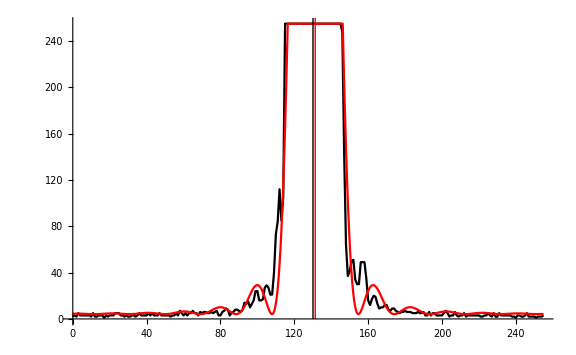

```mathematica
Show[{
ListPlot[observation,PlotRange->All,Joined->True,PlotStyle->Black],
Plot[fittedImx[x],{x,0,255},PlotRange->All, PlotStyle->Red]},
Epilog-> {
Black,Line[{{m,0},{m,300}}],
Red,Line[{{x0/.fittedImx["BestFitParameters"],0},{x0/.fittedImx["BestFitParameters"],300}}]},
ImageSize->Large]
```

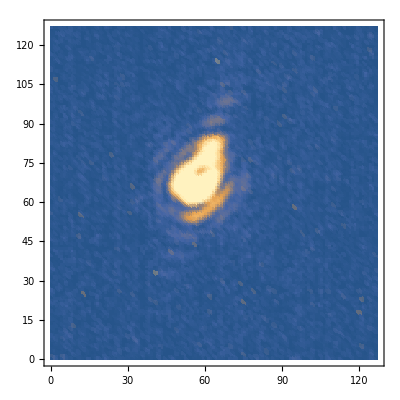

```mathematica
laserdata=Import["C:\\Users\\Benjamin\\OneDrive\\Documents\\UQAR\\2017 Été\\Stage I\\mathematica-test\\laser3.bmp", "RawData"];
side=Length[laserdata];
size=side*side;
lasermatrix=Table[0,size,3];
lasermatrix⟦All,1⟧=Table[Quotient[i,side],{i,0,size-1}];
lasermatrix⟦All,2⟧=Table[Mod[i,side],{i,0,size-1}];
lasermatrix⟦All,3⟧=Flatten[laserdata];
ListDensityPlot[lasermatrix, PlotRange->All]
```

```mathematica
fittedIx3D=NonlinearModelFit[lasermatrix,Ix3D[x,y,sx,sy,sz,x0,y0,z0],{{sx,2},{sy,2},{sz,255},{x0,side/2},{y0,side/2} ,{z0,8}},{x,y}]
```

FittedModel[Ix3D[x,y,5.35441,7.16696,210.178,58.4313,69.3102,4.83073]]

```mathematica
fittedImx3D=NonlinearModelFit[lasermatrix,Imx3D[x,y,sx,sy,sz,x0,y0,z0],{{sx,2},{sy,2},{sz,30720},{x0,side/2},{y0,side/2} ,{z0,8}},{x,y}]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[Imx3D[x,y,1.68528,2.04865,8780.42,59.4503,67.152,5.91017]]

```mathematica
fittedFx3D=NonlinearModelFit[lasermatrix,Fx3D[x,y,sx,sy,sz,x0,y0,z0],{{sx,2},{sy,2},{sz,1},{x0,side/2},{y0,side/2} ,{z0,6}},{x,y}]
```

FittedModel[Fx3D[x,y,6.24306,6.97498,3.34796,64.,64.,6.10601]]

```mathematica
fittedFmx3D=NonlinearModelFit[lasermatrix,Fmx3D[x,y,sx,sy,sz,x0,y0,z0],{{sx,16},{sy,16},{sz,255},{x0,side/2},{y0,side/2} ,{z0,6}},{x,y}]
```

FittedModel[Fmx3D[x,y,6.71601,8.91075,155.097,58.4217,69.3495,6.40802]]

```mathematica
fittedGx3D=NonlinearModelFit[lasermatrix,Gx3D[x,y,e,sx,sy,sz,x0,y0,z0],{{e,2},{sx,16},{sy,16},{sz,255},{x0,side/2},{y0,side/2} ,{z0,6}},{x,y}]
```

NonlinearModelFit::ivar: … is not a valid variable.

NonlinearModelFit[{{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,3},{0,8,8},{0,9,8},{0,10,4},{0,11,1},{0,12,1},{0,13,3},{0,14,1},{0,15,4},{0,16,7},{0,17,4},{0,18,1},{0,19,7},{0,20,1},{0,21,8},{0,22,9},{0,23,1},{0,24,1},{0,25,8},{0,26,1},{0,27,15},{0,28,1},{0,29,1},16325,{127,99,1},{127,100,3},{127,101,1},{127,102,1},{127,103,1},{127,104,2},{127,105,6},{127,106,6},{127,107,5},{127,108,3},{127,109,7},{127,110,2},{127,111,1},{127,112,2},{127,113,1},{127,114,1},{127,115,7},{127,116,2},{127,117,2},{127,118,6},{127,119,1},{127,120,6},{127,121,1},{127,122,2},{127,123,12},{127,124,9},{127,125,1},{127,126,4},{127,127,1}},2,{x,y}]
 |  |  |  |

```mathematica
fittedGmx3D=NonlinearModelFit[lasermatrix,Gmx3D[x,y,e,sx,sy,sz,x0,y0,z0],{{e,2},{sx,16},{sy,16},{sz,255},{x0,side/2},{y0,side/2} ,{z0,6}},{x,y}]
```

NonlinearModelFit::ivar: … is not a valid variable.

NonlinearModelFit[{{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,3},{0,8,8},{0,9,8},{0,10,4},{0,11,1},{0,12,1},{0,13,3},{0,14,1},{0,15,4},{0,16,7},{0,17,4},{0,18,1},{0,19,7},{0,20,1},{0,21,8},{0,22,9},{0,23,1},{0,24,1},{0,25,8},{0,26,1},{0,27,15},{0,28,1},{0,29,1},16325,{127,99,1},{127,100,3},{127,101,1},{127,102,1},{127,103,1},{127,104,2},{127,105,6},{127,106,6},{127,107,5},{127,108,3},{127,109,7},{127,110,2},{127,111,1},{127,112,2},{127,113,1},{127,114,1},{127,115,7},{127,116,2},{127,117,2},{127,118,6},{127,119,1},{127,120,6},{127,121,1},{127,122,2},{127,123,12},{127,124,9},{127,125,1},{127,126,4},{127,127,1}},2,{x,y}]
 |  |  |  |

```mathematica
ListDensityPlot[lasermatrix,PlotRange->All,
ImageSize->500,
Epilog->{
Red,Point[{x0/.fittedIx3D["BestFitParameters"],y0/.fittedIx3D["BestFitParameters"]}],
Green,Point[{x0/.fittedFx3D["BestFitParameters"],y0/.fittedFx3D["BestFitParameters"]}],
Blue,Point[{x0/.fittedGx3D["BestFitParameters"],y0/.fittedGx3D["BestFitParameters"]}],
RGBColor[255,0,255],Point[{x0/.fittedImx3D["BestFitParameters"],y0/.fittedImx3D["BestFitParameters"]}],
RGBColor[255,255,0],Point[{x0/.fittedFmx3D["BestFitParameters"],y0/.fittedFmx3D["BestFitParameters"]}],
RGBColor[0,255,255],Point[{x0/.fittedGmx3D["BestFitParameters"],y0/.fittedGmx3D["BestFitParameters"]}]}]
```

NonlinearModelFit::ivar: … is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::ivar: … is not a valid variable.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::ivar: … is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

-Graphics-

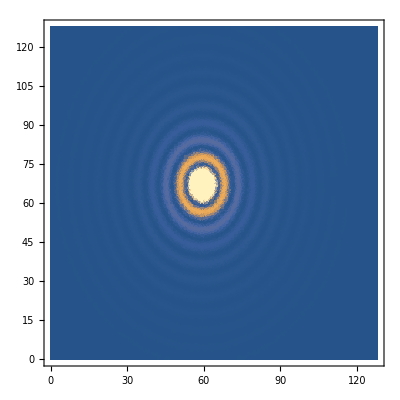

Plot3D::plln: Limiting value side in {Charting`Private`pvar$23496,0,side} is not a machine-sized real number.

ListPlot3D::arrayerr: lasermatrix must be a valid array or a list of valid arrays.

Show::gcomb: Could not combine the graphics objects in Show[Plot3D[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange→{0,255},PlotPoints→50],ListPlot3D[lasermatrix,PlotStyle→{RGBColor[0, 0, 1],Opacity[0.5]}]].

Plot3D::plln: Limiting value side in {Charting`Private`pvar$23566,0,side} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot3D[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange→{0,255},PlotPoints→50],ListPlot3D[lasermatrix,PlotStyle→{RGBColor[0, 0, 1],Opacity[0.5]}]].

Plot3D::plln: Limiting value side in {Charting`Private`pvar$25881,0,side} is not a machine-sized real number.

ListPlot3D::arrayerr: lasermatrix must be a valid array or a list of valid arrays.

Show::gcomb: Could not combine the graphics objects in Show[Plot3D[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange→{0,255},PlotPoints→50],ListPlot3D[lasermatrix,PlotStyle→{RGBColor[0, 0, 1],Opacity[0.5]}]].

Plot3D::plln: Limiting value side in {Charting`Private`pvar$25933,0,side} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot3D[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange→{0,255},PlotPoints→50],ListPlot3D[lasermatrix,PlotStyle→{RGBColor[0, 0, 1],Opacity[0.5]}]].

```mathematica
Manipulate[Show[Plot3D[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange->{0,255},PlotPoints->50],ListPlot3D[lasermatrix,PlotStyle->{Blue,Opacity[0.5]}]],{sx,2,32},{sy,2,32},{{sz,6000},0,100000},{{x0,31},0,64},{{y0,32.5},0,64},{{z0,8},-255,255}]
DensityPlot[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange->{0,255},PlotPoints->50]
```

```mathematica
Plot3D[fittedIx3D[x,y],{x,0,side},{y,0,side},PlotRange->All]
Plot3D[fittedGx3D[x,y],{x,0,side},{y,0,side},PlotRange->All]
Plot3D[fittedFx3D[x,y],{x,0,side},{y,0,side},PlotRange->All]
Plot3D[fittedImx3D[x,y],{x,0,side},{y,0,side},PlotRange->All]
Plot3D[fittedGmx3D[x,y],{x,0,side},{y,0,side},PlotRange->All]
Plot3D[fittedFmx3D[x,y],{x,0,side},{y,0,side},PlotRange->All]
```

-Graphics3D-

NonlinearModelFit::ivar: … is not a valid variable.

RandomReal::unifr: The endpoints specified by {-1. ϵ,ϵ} for the endpoints of the uniform distribution range are not real-valued.

General::stop: Further output of RandomReal::unifr will be suppressed during this calculation.

NonlinearModelFit::ivar: {Max[β,501.326 norm[0.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[0.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[1.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[1.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[2.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],«41»,Max[β,501.326 norm[23.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[23.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[24.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[24.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],«151»} is not a valid variable.

NonlinearModelFit::ivar: … is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-

-Graphics3D-

NonlinearModelFit::ivar: … is not a valid variable.

RandomReal::unifr: The endpoints specified by {-1. ϵ,ϵ} for the endpoints of the uniform distribution range are not real-valued.

General::stop: Further output of RandomReal::unifr will be suppressed during this calculation.

NonlinearModelFit::ivar: {Max[β,501.326 norm[0.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[0.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[1.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[1.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[2.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],«41»,Max[β,501.326 norm[23.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[23.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[24.,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],Max[β,501.326 norm[24.5,25.,1.]]+RandomReal[{-1. ϵ,ϵ}],«151»} is not a valid variable.

NonlinearModelFit::ivar: … is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-